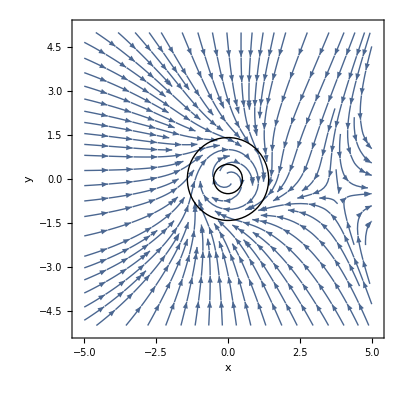

```mathematica
f[x_,y_]:=x*(1-x^2-y^2) +2*y +(x^4)/4;
g[x_,y_]:=-2x + y*(1-x^2-y^2);
p1 = StreamPlot[{f[x,y],g[x,y]},{x,-5,5},{y,-5,5},FrameLabel->{x,y}];
p2 = Graphics[Circle[{0,0}, Sqrt[2]]];
p3 = Graphics[Circle[{0,0}, 1/2]];
Show[p1,p2, p3]
```

```mathematica
Solve[f[x,y]==0 && g[x,y] ==0, {x,y}, Reals]
```

{{x→0,y→0},{x→Root[-1280-64 #1^3-128 #1^5+4 #1^8-4 #1^10+#1^11&,1],y→-4/3 Root[-1280-64 #1^3-128 #1^5+4 #1^8-4 #1^10+#1^11&,1]+5/6 Root[-1280-64 #1^3-128 #1^5+4 #1^8-4 #1^10+#1^11&,1]^2-5/6 Root[-1280-64 #1^3-128 #1^5+4 #1^8-4 #1^10+#1^11&,1]^3+1/24 Root[-1280-64 #1^3-128 #1^5+4 #1^8-4 #1^10+#1^11&,1]^4-1/6 Root[-1280-64 #1^3-128 #1^5+4 #1^8-4 #1^10+#1^11&,1]^5-1/24 Root[-1280-64 #1^3-128 #1^5+4 #1^8-4 #1^10+#1^11&,1]^6+1/24 Root[-1280-64 #1^3-128 #1^5+4 #1^8-4 #1^10+#1^11&,1]^7-1/24 Root[-1280-64 #1^3-128 #1^5+4 #1^8-4 #1^10+#1^11&,1]^8+1/48 Root[-1280-64 #1^3-128 #1^5+4 #1^8-4 #1^10+#1^11&,1]^9-5/384 Root[-1280-64 #1^3-128 #1^5+4 #1^8-4 #1^10+#1^11&,1]^10+1/384 Root[-1280-64 #1^3-128 #1^5+4 #1^8-4 #1^10+#1^11&,1]^11}}